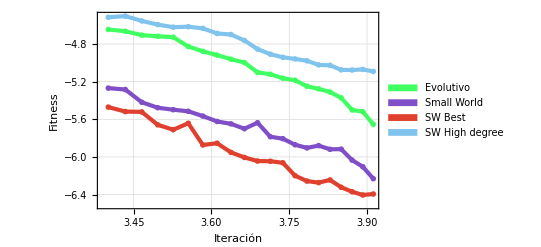

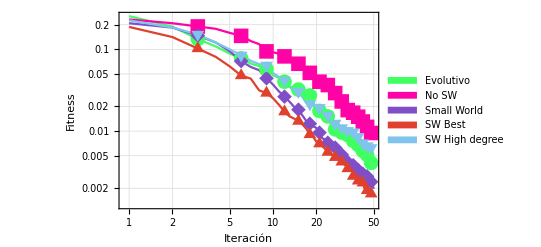

```mathematica
evolutivo = {0.254739054,0.189462608,0.133606895,0.108439337,0.088669032,0.077462437,0.066948987,0.062361605,0.057442723,0.048174630,0.044720106,0.040209922,0.035121634,0.034016834,0.032191800,0.030204317,0.029875109,0.027237370,0.023088190,0.017784220,0.017668375,0.015824934,0.015579118,0.015121505,0.012595590,0.011440986,0.010518749,0.009964202,0.009711489,0.009601178,0.009422874,0.009040622,0.008935265,0.008849618,0.008010181,0.007612584,0.007310184,0.007003303,0.006757181,0.006087490,0.005966119,0.005717470,0.005601382,0.005246925,0.005109842,0.004938664,0.004642655,0.004083422,0.004010912,0.003503731};
nosw = {0.231907542,0.208506722,0.190482152,0.178162396,0.158949991,0.146146206,0.126173063,0.115679969,0.094426434,0.092256191,0.088116447,0.082021601,0.076279259,0.066908320,0.066637981,0.063270297,0.055715435,0.051559630,0.046582611,0.042296002,0.040198705,0.039767629,0.037759859,0.036560846,0.034604636,0.030093820,0.029172155,0.025614135,0.024852018,0.023050142,0.020594964,0.019106029,0.018070843,0.017875257,0.016993486,0.016786024,0.015826448,0.015416351,0.014998999,0.013270629,0.013041906,0.013093388,0.012677361,0.011616535,0.011261621,0.010563027,0.010108895,0.009480595,0.009444126,0.009217624};
sw={0.208510538,0.184516521,0.147585820,0.121199721,0.094715043,0.071703128,0.060865478,0.055600078,0.044240938,0.037018991,0.030490799,0.026390603,0.022941266,0.019811226,0.018302078,0.015508466,0.013293512,0.012318686,0.011495647,0.010882047,0.009577595,0.008118708,0.007940900,0.007208715,0.007033647,0.006709765,0.006285271,0.005551429,0.005218639,0.005150513,0.005072319,0.004431634,0.004181344,0.004094339,0.004025970,0.003824925,0.003613577,0.003523156,0.003345595,0.003565020,0.003071530,0.003009784,0.002821583,0.002729019,0.002795662,0.002688737,0.002693580,0.002395988,0.002233123,0.001966979};
swbest = {0.187930694,0.141220005,0.102324929,0.080824275,0.061827006,0.047830889,0.043814394,0.031498410,0.029236037,0.025217804,0.020939830,0.017288839,0.015160150,0.014236036,0.013259553,0.012063006,0.010719892,0.009105715,0.008494301,0.007407332,0.007017681,0.006553854,0.006045597,0.005533787,0.005288440,0.005048763,0.004782673,0.004666339,0.004518778,0.004209641,0.004013969,0.003999941,0.003486760,0.003310328,0.003544717,0.002814739,0.002867766,0.002602076,0.002465694,0.002373411,0.002367770,0.002329694,0.002031462,0.001918085,0.001887164,0.001941290,0.001796005,0.001712757,0.001654439,0.001672193};
swhd ={0.226023283,0.185156471,0.151754336,0.121105871,0.099810792,0.084466497,0.072389162,0.065974640,0.063657817,0.051218862,0.045944007,0.041658373,0.034878010,0.030691131,0.030472903,0.026073774,0.022100722,0.021431625,0.020456387,0.019705877,0.019304062,0.017672361,0.015133390,0.015591181,0.013971189,0.013478757,0.012429205,0.012464446,0.011527854,0.010929193,0.011064423,0.010513804,0.010113204,0.009838893,0.009888761,0.009716821,0.009204317,0.009099301,0.008545818,0.007792405,0.007385237,0.007145283,0.007019701,0.006884474,0.006587174,0.006563291,0.006249784,0.006241093,0.006282055,0.006147876};


ListLogLogPlot[{evolutivo[[30;;50]],sw[[30;;50]],swbest[[30;;50]],swhd[[30;;50]]},Joined->True,PlotRange->Full, DataRange->{30,50}, GridLines->Automatic, FrameTicksStyle->Directive[Black,15],Frame->{{True,False},{True,False}},FrameLabel->{Style["Iteración",Black,Large],Style["Fitness",Black,Large]},PlotLegends->SwatchLegend[{"Evolutivo","Small World","SW Best","SW High degree"}], PlotTheme->"Business", PlotStyle->{RGBColor[0.25,1,0.38],RGBColor[0.5,0.31,0.78], RGBColor[0.88,0.25,0.18],RGBColor[0.5,0.77,0.93]}]

ListLogLogPlot[{evolutivo,nosw,sw,swbest,swhd},Joined->True,PlotRange->Full,GridLines->Automatic, FrameTicksStyle->Directive[Black,15], Frame->{{True,False},{True,False}},FrameLabel->{Style["Iteración",Black,Large],Style["Fitness",Black,Large]},PlotLegends->SwatchLegend[{"Evolutivo","No SW","Small World","SW Best","SW High degree"}],Mesh->{Range[0,50,3]},PlotMarkers->{Automatic,15},PlotStyle->{RGBColor[0.25,1,0.38],RGBColor[1,0.01,0.65],RGBColor[0.5,0.31,0.78], RGBColor[0.88,0.25,0.18],RGBColor[0.5,0.77,0.93],Thickness[0.008]}]
```